## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs2=GenAll[2];Length[baseGraphs2]
```

3

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 2 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations2=CompleteRelations[baseGraphs2];Length[withRelations2]
```

3

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 15 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations2[k,"graph"],k],{k,Keys[withRelations2]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs2=Select[Reverse[Keys[withRelations2]],CompleteGraphQ[withRelations2[#,"graph"]]&];Length[completeGraphs2]
```

2

```mathematica
baseGraphAxioma2=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations2[k,"vertexsets"]],{k,completeGraphs2}]]
```

{x2→v12,x1→v1x2}

Now we get some lists of variables

```mathematica
allGraphVariables2=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations2]}];Length[allGraphVariables2]
```

3

```mathematica
baseGraphAxioma2Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma2]]]];Length[baseGraphAxioma2Vars]
```

2

```mathematica
baseKeys2=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma2]
```

{2,1}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7207 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations2[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma2],
{key,baseKeys2}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 52 base variables.
This procedure only works fior the b01... variables since we need 5 vertices for the current implementation

```mathematica
withColorTables2=withRelations2;
```

```mathematica
GenerateColorTable2[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[2],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable2[withColorTables2,2]
```

{{v12,0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys2=baseKeys2;
```

```mathematica
baseGraphAxioma2Vars
```

{v12,v1x2}

```mathematica
Monitor[Table[
withColorTables2[k]["colortable"]=GenerateColorTable2[withColorTables2,k]
,
{k,baseGraphKeys2}
],k];
```

```mathematica
Keys[withColorTables2[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colofour,colortable}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable2[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables2[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables2[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables2[r1],"colortable"],
withColorTables2[r1,"colortable"]=TryComputeColourTable2[r1],
];
If[!KeyExistsQ[withColorTables2[r2],"colortable"],
withColorTables2[r2,"colortable"]=TryComputeColourTable2[r2],

];
withColorTables2[k,"colortable"]=withColorTables2[r1,"colortable"]+withColorTables2[r2,"colortable"];
withColorTables2[k,"colofour"]=withColorTables2[r1,"colofour"]+withColorTables2[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables2[k]["relations"]}
]
];
withColorTables2[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables2[0],"colortable"]
```

False

```mathematica
TryComputeColourTable2[0]
```

{{v12,v1x2}}

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables2[k]["colortable2"]=withColorTables2[k]["colortable"]
,
{k,Keys[withColorTables2]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp2=withColorTables2;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp2[k,"comp"]=GreaterEqual;withRelations2[k,"comp"]="No IH";k,{k,Keys[withComp2]}]//Length
```

3

```mathematica
CosyPrint2[key_]:=With[
{current=withComp2[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

```mathematica
ColofourPrint2[key_]:=With[
{current=withComp2[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{70,70}]
}
],
{Style[current["signature"],First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]->TraditionalForm[current["colofour"]],ChromaticPolynomial[current["graph"],4]/24}]]]
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right],
 result=current},
(*Print[currentS,"  ", leftS, "  ", rightS];*)
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
]
];
result
]
```

```mathematica
RecalculateComp2[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp2[k];
If[depth<maxdepth && ! current["marked"],
withComp2[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];


withComp2[r1,"parents"]=Append[withComp2[r1,"parents"],k];
withComp2[r2,"parents"]=Append[withComp2[r2,"parents"],k];
withComp2[k,"children"]=Append[withComp2[k,"children"],{r1,r2}];

RecalculateComp2[r1,depth+1,maxdepth];
RecalculateComp2[r2,depth+1,maxdepth];
withComp2[k,"comp"]= MayBeReassign[k,withComp2[k,"comp"], withComp2[r1,"comp"],withComp2[r2,"comp"]]
];
]
,{r,withComp2[k]["relations"]}
];
];withComp2[k,"comp"]
]
```

```mathematica
Table[withComp2[k,"marked"]=False;withComp2[k,"parents"]={};withComp2[k,"children"]={};k,{k,Keys[withComp2]}];markCount=0
```

0

```mathematica
IsPlanarSet[set_,total_]:=Block[{result,sot=set-1,breaks=0,i,previous},
If[Length[set]==1,
result=True,
For[i=2,i≤Length[sot],i++,
If[Mod[sot[[i-1]]+1,total]≠Mod[sot[[i]],total],
breaks++;
]
];
If[Mod[sot[[Length[sot]]]+1,total]≠Mod[sot[[1]],total],
breaks++;
];
result=breaks<2;
];
result
]
```

```mathematica
IsPlanarContraction[assoc_,key_]:=Block[{total},
total=Length[Flatten[assoc[key,"vertexsets"]]];
Fold[And,Table[IsPlanarSet[s,total],{s,assoc[key,"vertexsets"]}]]
];
```

```mathematica
Table[If[
IsPlanarContraction[withComp2,k],
withComp2[k,"comp"]=Greater;
withComp2[k,"compwhy"]="Planar contraction";
1,
0]
,{k,baseKeys2}]
```

{1,1}

```mathematica
Table[withComp2[k,"comp"]=Equal;withComp2[k,"compwhy"]="Contains K Five";k,{k,Select[baseKeys2,!PlanarGraphQ[withComp2[#,"graph"]]&]}]//Length
```

0

```mathematica
Monitor[
Table[If[
PlanarGraphQ[EmbedGraph2[withComp2,key]],
If[ToString[withComp2[key]["comp"]]=="GreaterEqual",
withComp2[key]["compwhy"]="Embedding is planar and follows IH";withComp2[key]["comp"]=Greater;
1,
0],
0
],{key,Keys[withComp2]}],
key]//Total
```

0

```mathematica
markCount=0
```

0

```mathematica
Monitor[RecalculateComp2[0,0,20],markCount]
```

Greater

```mathematica
Select[Keys[withComp2],withComp2[#,"comp"]==Greater&]//Length
```

3

```mathematica
41579
```

41579

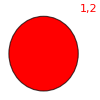
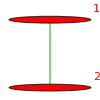
{-Graphics-{2→v12,1/6},-Graphics-{1→v1x2,1/2}}

```mathematica
Table[CosyPrint2[k],{k,baseKeys2}]
```

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm2=withComp2;
```

```mathematica
Keys[stubbornForm2[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colofour,colortable,colortable2,comp,marked,parents,children,compwhy}

```mathematica
stubbornKeys2 = Select[Keys[stubbornForm2],(ToString[stubbornForm2[#]["comp"]]=="GreaterEqual")&];Length[stubbornKeys2]
```

0

```mathematica
Intersection[baseKeys2,stubbornKeys2]//Length
```

0

```mathematica
CosyPrintThree2[key_]:=ColorTablePrint[key,stubbornForm2,"colofour","colortable"]
```

```mathematica
ineqsthree2=Monitor[Table[stubbornForm2[k]["comp"][stubbornForm2[k]["colofour"],0],{k,Keys[stubbornForm2]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsthree2]
```

3

```mathematica
ineqsthree22=Fold[And,ineqsthree2]//Simplify
```

v12>0&&v1x2>0

```mathematica
ExpressionToTable[ineqsthree22]
```

v12>0
v1x2>0